```mathematica
(1-a[x])p[x]+a[x]q[x]
```

(1-a[x]) p[x]+a[x] q[x]

```mathematica
FullSimplify[
Normalize[{x,f[x]}].
Normalize[{x,g[x]}]
,{x,f[x],g[x]}∈Reals]
```

(x^2+f[x] g[x])/(√((x^2+f[x]^2) (x^2+g[x]^2)))

```mathematica
(1-a[x]) f[x]+a[x] g[x]
```

(1-a[x]) f[x]+a[x] g[x]

```mathematica
With[{a=Function[x,x]},
(1-a[x]) f[x]+a[x] g[x]
]
```

(1-x) f[x]+x g[x]

```mathematica
With[{a=Function[x,(x^2+f[x] g[x])/(√((x^2+f[x]^2) (x^2+g[x]^2)))]},
(1-a[x]) f[x]+a[x] g[x]
]
```

(g[x] (x^2+f[x] g[x]))/(√((x^2+f[x]^2) (x^2+g[x]^2)))+f[x] (1-(x^2+f[x] g[x])/(√((x^2+f[x]^2) (x^2+g[x]^2))))

```mathematica
FullSimplify[
(g[x] (x^2+f[x] g[x]))/(√((x^2+f[x]^2) (x^2+g[x]^2)))+f[x] (1-(x^2+f[x] g[x])/(√((x^2+f[x]^2) (x^2+g[x]^2))))
,{x,f[x],g[x]}∈Reals]
```

f[x]-(f[x] (x^2+f[x] g[x]))/(√((x^2+f[x]^2) (x^2+g[x]^2)))+(g[x] (x^2+f[x] g[x]))/(√((x^2+f[x]^2) (x^2+g[x]^2)))

```mathematica
f[x]==f[x-1]+1
```

f[x]==1+f[-1+x]

```mathematica
f[x]==x
```

f[x]==x

```mathematica
RSolve[{f[x]==f[x-1]+1,f[0]==0},f[x],x]
```

{{f[x]→x}}

```mathematica
f[x]==(1-a[x])p[x]+a[x]q[x]
```

f[x]==(1-a[x]) p[x]+a[x] q[x]

```mathematica
With[{f=Function[x,x^2]},
f[x]==(1-a[x]) p[x]+a[x] q[x]
]
```

x^2==(1-a[x]) p[x]+a[x] q[x]

```mathematica
With[{f=Function[x,x^2],a=Function[x,(1+Cos[π x])/x]},
f[x]==(1-a[x]) p[x]+a[x] q[x]
]
```

x^2==(1-(1+Cos[π x])/x) p[x]+((1+Cos[π x]) q[x])/x

```mathematica
With[{f=Function[x,x^2],a=Function[x,(1+Cos[π x])/x],p=Identity},
f[x]==(1-a[x]) p[x]+a[x] q[x]
]
```

x^2==x (1-(1+Cos[π x])/x)+((1+Cos[π x]) q[x])/x

```mathematica
Reduce[x^2==x (1-(1+Cos[π x])/x)+((1+Cos[π x]) q[x])/x]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[x^2==x (1-(1+Cos[π x])/x)+((1+Cos[π x]) q[x])/x]

```mathematica
Solve[x^2==x (1-(1+Cos[π x])/x)+((1+Cos[π x]) q[x])/x,q[x],Reals]
```

{{q[x]→ConditionalExpression[(-x+x^2-x^3-x Cos[π x])/(-1-Cos[π x]),(C[1]∈ℤ&&-1<x<0)||(C[1]∈ℤ&&0<x<1)||(C[1]∈ℤ&&-1<x-2 C[1]<1&&C[1]≥1)||(C[1]∈ℤ&&-1<x-2 C[1]<1&&C[1]≤-1)]}}

```mathematica
(-x+x^2-x^3-x Cos[π x])/(-1-Cos[π x])
```

(-x+x^2-x^3-x Cos[π x])/(-1-Cos[π x])

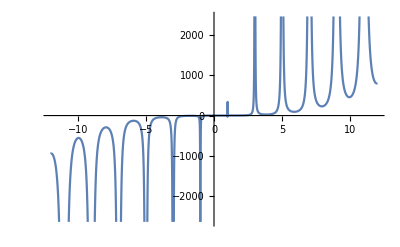

```mathematica
Plot[(-x+x^2-x^3-x Cos[π x])/(-1-Cos[π x]),{x,-12.,12.}]
```

```mathematica
Solve[x^2==x (1-(1+Cos[π x])/x)+((1+Cos[π x]) q[x])/x,q[x]]
```

{{q[x]→(x (1-x+x^2+Cos[π x]))/(1+Cos[π x])}}

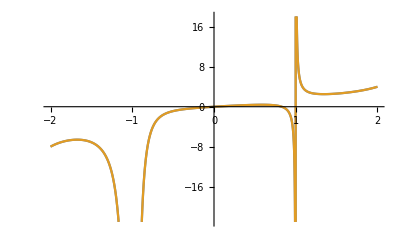

```mathematica
Plot[
{(-x+x^2-x^3-x Cos[π x])/(-1-Cos[π x]),(x (1-x+x^2+Cos[π x]))/(1+Cos[π x])}
,{x,-2,2}]
```

```mathematica
(-x+x^2-x^3-x Cos[π x])/(-1-Cos[π x])==(x (1-x+x^2+Cos[π x]))/(1+Cos[π x])
```

(-x+x^2-x^3-x Cos[π x])/(-1-Cos[π x])==(x (1-x+x^2+Cos[π x]))/(1+Cos[π x])

```mathematica
Reduce[(-x+x^2-x^3-x Cos[π x])/(-1-Cos[π x])==(x (1-x+x^2+Cos[π x]))/(1+Cos[π x])]
```

True

```mathematica
f[x]==(1-a[x]) p[x]+a[x] q[x]
```

f[x]==(1-a[x]) p[x]+a[x] q[x]

```mathematica
(1-((1+Cos[π x])/2))(x)+((1+Cos[π x])/2)(x (1-x+x^2+Cos[π x]))/(1+Cos[π x])
```

x (1+1/2 (-1-Cos[π x]))+1/2 x (1-x+x^2+Cos[π x])

```mathematica
FullSimplify[x (1+1/2 (-1-Cos[π x]))+1/2 x (1-x+x^2+Cos[π x])]
```

1/2 x (2+(-1+x) x)

```mathematica
Expand[1/2 x (2+(-1+x) x)]
```

x-x^2/2+x^3/2

```mathematica
A == x y
```

A==x y

```mathematica
Dt[A==x y]
```

Dt[A]==y Dt[x]+x Dt[y]

```mathematica
1+2
```

3

```mathematica
Attributes[==]
```

```mathematica
Attributes@Equal
```

{Protected}

```mathematica
D[f[x],x]
```

f'[x]

```mathematica
D[f[g[x]],x]
```

f'[g[x]] g'[x]

```mathematica
Dt[f[g[x]]]
```

Dt[x] f'[g[x]] g'[x]

```mathematica
D[f[g[h[x]]],x]
```

f'[g[h[x]]] g'[h[x]] h'[x]

```mathematica
Dt[f[x]]
```

Dt[x] f'[x]

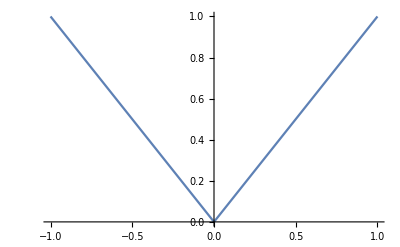

```mathematica
Plot[Abs@x,{x,-1,1}]
```

```mathematica
(√x)^2
```

x

```mathematica
√(x^2)
```

√(x^2)

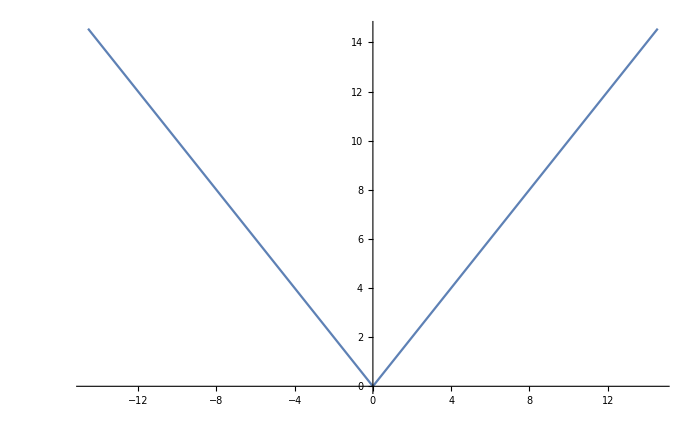

```mathematica
Plot[√(x^2),{x,-14.56,14.56}]
```

```mathematica
D[√(x^2),x]
```

x/(√(x^2))

```mathematica
FullForm[Sqrt,Power[2]]
```

FullForm::nonopt: Options expected (instead of 2) beyond position 1 in FullForm[Sqrt,2]. An option must be a rule or a list of rules.

FullForm[Sqrt,2]

```mathematica
FullForm[Sqrt,Power[#,2]&]
```

FullForm::nonopt: Options expected (instead of #1^2&) beyond position 1 in FullForm[Sqrt,#1^2&]. An option must be a rule or a list of rules.

FullForm[Sqrt,#1^2&]

```mathematica
FullForm[Composition[Sqrt,Power[#,2]&]]
```

Composition[Sqrt,Function[Power[Slot[1],2]]]

```mathematica
√(x^2)
```

√(x^2)

```mathematica
FullForm@√(x^2)
```

Power[Power[x,2],Rational[1,2]]

```mathematica
Power[Power[x,2],Rational[1,2]]
```

```mathematica
Sqrt[Power[x,2]]
```

```mathematica
Sqrt[Power[x,2]]
```

√(x^2)

```mathematica
Power[Power[x,2],Rational[1,2]]
```

√(x^2)

```mathematica
Power[Power[x,2],Rational[1,2]]== Sqrt[Power[x,2]]
```

True

```mathematica
D[√(x^2),x]
```

x/(√(x^2))

```mathematica
Limit[x/(√(x^2)),x->0]
```

Indeterminate

```mathematica
With[{x=δ},
x/(√(x^2))
]
```

δ/(√(δ^2))

```mathematica
With[{x=δ+1},
x/(√(x^2))
]
```

(1+δ)/(√((1+δ)^2))

```mathematica
With[{x=δ+1},
x/(√(x^2))
]
```

```mathematica
Abs[Abs[x]-f[x]]≤0
```

Abs[Abs[x]-f[x]]≤0

```mathematica
Abs[Abs[x]-f[x]]==0
```

Abs[Abs[x]-f[x]]==0

```mathematica
TraditionalForm@Abs[Abs[x]-f[x]]==0
```

Abs[Abs[x]-f(x)]==0

```mathematica
√(x^2)
```

√(x^2)

```mathematica
√(x^2+1)
```

√(1+x^2)

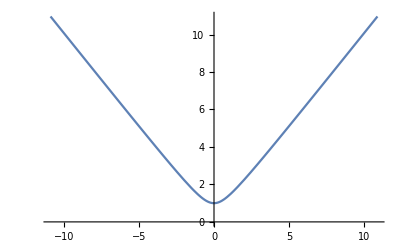

```mathematica
Plot[√(1+x^2),{x,-10.92,10.92}]
```

```mathematica
√(x^2+1)-f[x]==x
```

√(1+x^2)-f[x]==x

```mathematica
Reduce[√(1+x^2)-f[x]==x]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[√(1+x^2)-f[x]==x]

```mathematica
√(x^2+1)-1
```

-1+√(1+x^2)

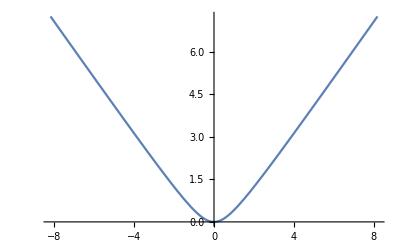

```mathematica
Plot[-1+√(1+x^2),{x,-8.19,8.19}]
```

```mathematica
√(x^2+1)-√1
```

-1+√(1+x^2)

```mathematica
-1+√(1+x^2)
```

```mathematica
Solve[x^2+1,x,Reals]
```

Solve::naqs: 1+x^2 is not a quantified system of equations and inequalities.

Solve[1+x^2,x,ℝ]

```mathematica
Solve[x^2+1==0,x,Reals]
```

{}

```mathematica
Solve[x^2+1==0,x,Reals]
```

```mathematica
Complexes
```

ℂ

```mathematica
Solve[x^2+1==0,x,Complexes]
```

{{x→-ⅈ},{x→ⅈ}}

```mathematica
ComplexPlot[x^2,{x,-2-2I,2+2I}]
```

-Graphics-

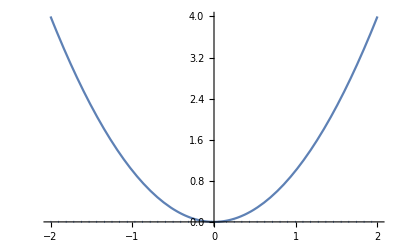

```mathematica
ReImPlot[x^2,{x,-2,2}]
```